## Calculating the firing velocity with Tracker

In this notebook we compare the tracker data with the Mathematica data. Also it requires concurrent running with the final notebook 1.

```mathematica
Tracker =Import["~/Desktop/FinalMathematica/mathematicaplot.csv"];(*Change path here*)
```

```mathematica
Tracker=Drop[Tracker,2];
```

```mathematica
Pos=Table[{Tracker[[i,2]],Tracker[[i,3]]},{i,1,Length[Tracker] }];
```

This the tracker data for the position. The axes are inverted and the scale is off.

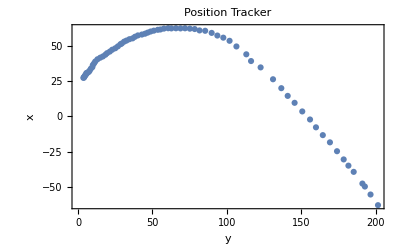

```mathematica
ListPlot[Pos,PlotLabel-> "Position Tracker",Frame->True,FrameLabel->{"y","x"}]
```

This is the position plot of the Mathematica model.

```mathematica
lis=Table[{xpos[t],ypos[t]},{t,0,.5,.001}];
```

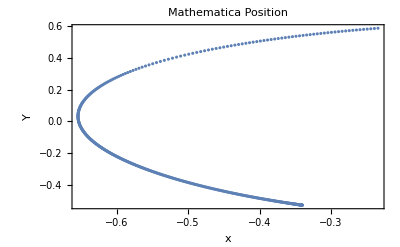

```mathematica
ListPlot[lis,PlotLabel-> "Mathematica Position",Frame->True,FrameLabel->{"x","Y"}]
```

```mathematica
vel= Drop[Table[{Tracker[[i,4]],Tracker[[i,5]]},{i,1,Length[Tracker] }],1];
```

Here I use the tracker data. The time has to be scaled by 1/4 and the velocity by 1/40. (Those are approximate scaling factors. )

```mathematica
velf = Table[{Tracker[[i+1,1]]/4,1/40  *Tracker[[i,6]]},{i,1,Length[vel]}]
```

```mathematica
velf =Insert[velf, {0,0},1];
```

```mathematica
Track=ListPlot[velf, Joined->True,PlotLabel-> "Comparison Velocity over time ",Frame->True,FrameLabel->{"t ","v"},PlotRange->{{0,.5},{0,10}},PlotStyle->Red];
```

```mathematica
Mathem = Plot[Sqrt[vxpro[t]^2+vypro[t]^2],{t,0,.5}];
```

This graph compares the tracker data with the Mathematica data. The red is Mathematica and the blue is the Mathematica plot. The difference between the peaks could be due to an erroneous scaling factor.

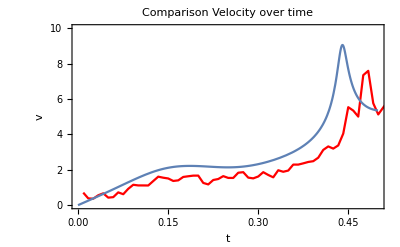

```mathematica
Show[ Track,Mathem]
```